# Form Factors

## Init

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
<<"funcs.m"
```

```mathematica
<<"./mdat/amps.mdat";
```

## Ebert

```mathematica
json = Import["../literatute/Ebert_1007.1369/Fig3.json"];
```

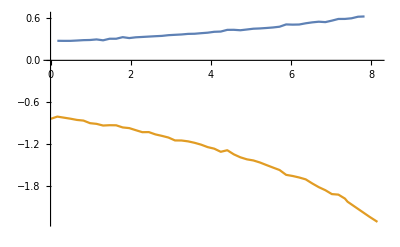

```mathematica
tab$fMinus = extractFF[json,1,-1]["data"];
tab$fPlus = extractFF[json, 2]["data"];
ListPlot[{tab$fPlus, tab$fMinus}, Joined->True]
```

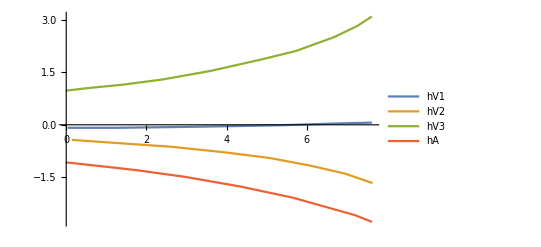

```mathematica
chic1 = Import["../literatute/Ebert_FFs/fig3_chic1_1P.json"];
tab$hV1 = extractFF[json,3]["data"];
tab$hV2 = extractFF[json,4, -1]["data"];
tab$hV3 = extractFF[json,5]["data"];
tab$hA = extractFF[json,6,-1]["data"];
ListPlot[{tab$hV1,tab$hV2,tab$hV3, tab$hA}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

```mathematica
extractNames[json]
```

(1 | -fMinus
2 | fPlus
3 | hV1
4 | -hV2
5 | hV3
6 | -hA
7 | tA3
8 | tA2
9 | -tA1
10 | -tV)

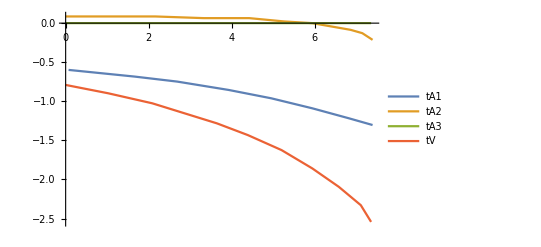

```mathematica
chic2 = Import["../literatute/Ebert_FFs/fig3_chic2_1P.json"];
tab$tA3 = extractFF[json, 7]["data"];
tab$tA2 = extractFF[json, 8]["data"];
tab$tA1 = extractFF[json, 9, -1]["data"];
tab$tV = extractFF[json, 10,-1]["data"];
ListPlot[{tab$tA1, tab$tA2, tab$tA3, tab$tV},Joined->True, PlotLegends->{"tA1", "tA2", "tA3", "tV"}, PlotRange->All]
```

```mathematica
ffFitRule = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]], fitFunc,fitParams,q2]]
,{ff, ffList}];
```

```mathematica
str="";
Do[
str=str<>"*"<>ToString[f⟦1,0⟧]<>"="<>ToString[CForm[f⟦2⟧/.Power->pow]]<>";\n"
,{f, ffFitRule}];
str
```

*fPlus=0.2682601722555334 + 0.02303968108048947*q2 + 0.0020380398181458516*pow(q2,2) + 0.00011294466805778708*pow(q2,3);
*fMinus=-0.7950384705178547 - 0.09246771336762735*q2 + 0.0010726158830268208*pow(q2,2) - 0.001481021602795487*pow(q2,3);
*hV1=-0.08704293492689502 - 0.0022986841192460623*q2 + 0.0038467447392757396*pow(q2,2) - 0.00012553804720134653*pow(q2,3);
*hV2=-0.41683490266687373 - 0.10099528570614397*q2 + 0.013784440542007744*pow(q2,2) - 0.002858592443737963*pow(q2,3);
*hV3=0.9684907205277232 + 0.15312199497069726*q2 - 0.014045366905842667*pow(q2,2) + 0.003943573898496621*pow(q2,3);
*hA=-1.0742257040633414 - 0.12413796805306339*q2 - 0.0008757292287017163*pow(q2,2) - 0.001569381021884598*pow(q2,3);
*tV=-0.7798067949888976 - 0.14162491575024025*q2 + 0.01663810403264435*pow(q2,2) - 0.003958812298323202*pow(q2,3);
*tA1=-0.5964590912173986 - 0.040651581481948015*q2 - 0.0053292989710398584*pow(q2,2) - 0.0002931697947718947*pow(q2,3);
*tA2=0.09336134379726901 - 0.033133225444554985*q2 + 0.016028359374336804*pow(q2,2) - 0.0022492990861063*pow(q2,3);
*tA3=0.;

```mathematica
DeleteFile["./mdat/ebert_ff.mdat"];
file = OpenWrite["./mdat/ebert_ff.mdat"];
WriteString[file, ToString[Definition[ffFitRule], InputForm]<>"\n"];
WriteString[file, ToString[Definition[ffFitRule$2P], InputForm]<>"\n"];
Close[file];
```

## Wang et al, arXiv:1107:0474 [hep-ph]

```mathematica
json = Import["../literatute/1107.0474/fig3_FF.json"];
```

```mathematica
(* we have distribution over q2max - q2 on the plot! *)
Clear[getMcc];
GeV=1.; MeV=10^-3 GeV;
$MBc = 6274.47MeV;
(* 1P masses from PDG *)
getMcc[out_, type_:"1P"]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
(* 2P masses are chosen to fit Ebert's distributions *)
getMcc[out_, "2P"]:=Switch[out,"chi_c0", 3862MeV,"chi_c1", 3.9214,"chi_c2",3.967735]
q2Max[out_]:=($MBc-getMcc[out])^2;
```

```mathematica
Clear[reflect];
reflect[tab_,out_]:=Module[{newTab=tab},
newTab⟦All,1⟧=q2Max[out]-newTab⟦All,1⟧;
newTab
];
```

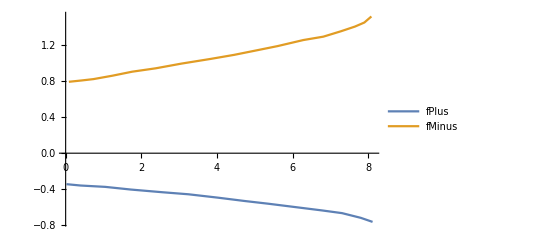

```mathematica
out="chi_c0";
tab$fPlus = extractFF[json, 1, -1]⟦"data"⟧//reflect[#,out]&;
tab$fMinus= extractFF[json, 2]⟦"data"⟧//reflect[#,out]&;
ListPlot[{tab$fPlus,tab$fMinus}, Joined->True, PlotLegends->{"fPlus","fMinus"}]
```

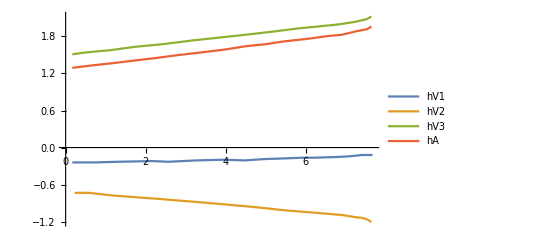

```mathematica
out="chi_c1";
tab$hV1 = extractFF[json, 3, -1]⟦"data"⟧//reflect[#,out]&;
tab$hV2 = extractFF[json, 4, -1]⟦"data"⟧//reflect[#,out]&;
tab$hV3 = extractFF[json, 5 ]⟦"data"⟧//reflect[#,out]&;
tab$hA = extractFF[json, 6 ]⟦"data"⟧//reflect[#,out]&;
ListPlot[{tab$hV1,tab$hV2,tab$hV3, tab$hA}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

```mathematica
extractNames[json]
```

{{1,chi0: -sPlus},{2,chi0_sMinus},{3,chi1: -f},{4,chi1: -u1},{5,chi1:u2},{6,chi1:g},{7,chi2:-c1},{8,chi2:-k},{9,chi2:c2},{10,chi2:h}}

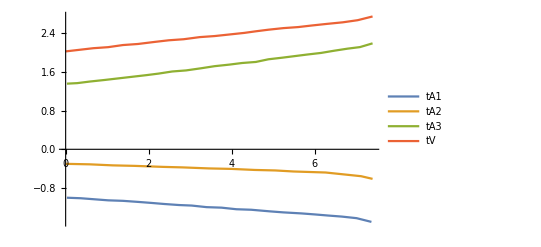

```mathematica
out="chi_c2";
tab$tA2 = extractFF[json, 7, -1]⟦"data"⟧//reflect[#,out]&;
tab$tA1 = extractFF[json, 8, -1]⟦"data"⟧//reflect[#,out]&;
tab$tA3 = extractFF[json, 9]⟦"data"⟧//reflect[#,out]&;
tab$tV = extractFF[json, 10]⟦"data"⟧//reflect[#,out]&;
ListPlot[{tab$tA1, tab$tA2, tab$tA3, tab$tV},Joined->True, PlotLegends->{"tA1", "tA2", "tA3", "tV"}, PlotRange->All]
```

```mathematica
fitFunc=a0+a1 q2 + a2 q2^2+a3 q2^3;
fitParams = DeleteCases[Variables[fitFunc] ,q2]
```

{a0,a1,a2,a3}

```mathematica
ffFitRule$Wang = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]], fitFunc,fitParams,q2]]
,{ff, ffList}]
```

{fPlus[q2_]:>-0.339914-0.0400244 q2+0.002523 q2^2-0.000465616 q2^3,fMinus[q2_]:>0.77019+0.088168 q2-0.00879204 q2^2+0.00108867 q2^3,hV1[q2_]:>-0.244354+0.0103316 q2-0.000913403 q2^2+0.000221592 q2^3,hV2[q2_]:>-0.710388-0.0602775 q2+0.00426655 q2^2-0.000565963 q2^3,hV3[q2_]:>1.49342+0.0899868 q2-0.00685796 q2^2+0.00071155 q2^3,hA[q2_]:>1.27202+0.090039 q2-0.00513732 q2^2+0.000614869 q2^3,tV[q2_]:>2.01927+0.101539 q2-0.00523579 q2^2+0.000591919 q2^3,tA1[q2_]:>-0.988895-0.068395 q2+0.00543166 q2^2-0.000688005 q2^3,tA2[q2_]:>-0.292165-0.0475703 q2+0.00992445 q2^2-0.00121872 q2^3,tA3[q2_]:>1.34214+0.101109 q2-0.00108563 q2^2+0.000339803 q2^3}

```mathematica
DeleteFile["./mdat/wang_ff.mdat"];
file = OpenWrite["./mdat/wang_ff.mdat"];
WriteString[file, ToString[Definition[ffFitRule$Wang], InputForm]<>"\n"];
Close[file];
```

```mathematica
str="// Wnang's FF\n\n";
Do[
str=str<>"*"<>ToString[f⟦1,0⟧]<>"="<>ToString[CForm[f⟦2⟧/.Power->pow]]<>";\n"
,{f, ffFitRule$Wang}]
str
```

// Wnang's FF

*fPlus=-0.33991380592027914 - 0.040024442563952885*q2 + 0.0025230010943415723*pow(q2,2) - 0.0004656159966881966*pow(q2,3);
*fMinus=0.7701897692262628 + 0.0881680421897945*q2 - 0.00879204111309994*pow(q2,2) + 0.0010886713551476884*pow(q2,3);
*hV1=-0.24435448046190159 + 0.010331648277938579*q2 - 0.0009134031378323107*pow(q2,2) + 0.00022159216585685204*pow(q2,3);
*hV2=-0.7103876821583478 - 0.0602774820822653*q2 + 0.004266553207625208*pow(q2,2) - 0.000565962924451258*pow(q2,3);
*hV3=1.4934249265375008 + 0.08998682725105182*q2 - 0.006857963573522601*pow(q2,2) + 0.000711550359979238*pow(q2,3);
*hA=1.2720231435712308 + 0.09003897439415781*q2 - 0.005137318246822382*pow(q2,2) + 0.0006148691245052408*pow(q2,3);
*tV=2.0192706161363225 + 0.10153860806900702*q2 - 0.0052357919072080665*pow(q2,2) + 0.0005919186313734745*pow(q2,3);
*tA1=-0.9888948657318037 - 0.0683950179746637*q2 + 0.005431661340191046*pow(q2,2) - 0.0006880049067587609*pow(q2,3);
*tA2=-0.2921648565036161 - 0.04757032020969248*q2 + 0.009924447477444942*pow(q2,2) - 0.0012187229555837636*pow(q2,3);
*tA3=1.3421413598569518 + 0.10110866108376225*q2 - 0.0010856339717409947*pow(q2,2) + 0.0003398028563210277*pow(q2,3);

## Henandez, hep-ph/0607150v3

```mathematica
json = Import["..//literatute/Hernandez_0607150/chi_c0.json"];
```

```mathematica
extractNames[json]
```

(1 | -fMinus
2 | fPlus)

```mathematica
<<"./mdat/amps.mdat";
```

```mathematica
P = p1+p2; q=p1-p2;
```

```mathematica
ScalarProduct[p2, eps]=0;
```

```mathematica
amplitude["chi_c1","V"]
```

hV1(q2) (MBc+Mcc) (ḡ)^amu+((OverBar[p1]-OverBar[p2])^a (hV2(q2) OverBar[p1]^mu+hV3(q2) OverBar[p2]^mu))/MBc

```mathematica
Pair[Momentum[p2],LorentzIndex[a]]=0;Pair[Momentum[p2],LorentzIndex[b]]=0;
```

```mathematica
out = "chi_c0";
ampH[out]=Calc[FV[P,mu]FPlus + FV[q,mu]Fminus]
```

Fminus OverBar[p1]^mu-Fminus OverBar[p2]^mu+FPlus OverBar[p1]^mu+FPlus OverBar[p2]^mu

```mathematica
diff = (ampH[out]-amplitude[out, "V+A"])//Calc//Collect[#, Pair[__]]&//ReplaceAll[#, a_[q2]:>a]&
Solve[#==0&/@(Select[#, FreeQ[#, Pair[__]]&]&/@List@@diff), {fPlus, fMinus}]
```

OverBar[p1]^mu (-fMinus+Fminus-fPlus+FPlus)+OverBar[p2]^mu (fMinus-Fminus-fPlus+FPlus)

{{fPlus→FPlus,fMinus→Fminus}}

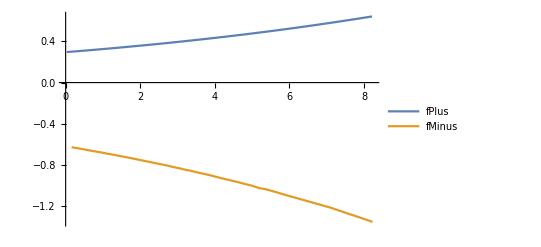

```mathematica
out="chi_c0";
tab$fMinus= extractFF[json, 1, -1]⟦"data"⟧;
tab$fPlus = extractFF[json, 2]⟦"data"⟧;
ListPlot[{tab$fPlus,tab$fMinus}, Joined->True, PlotLegends->{"fPlus","fMinus"}]
```

```mathematica
ffFitRule$Hernandez  = {};
```

```mathematica
AppendTo[ffFitRule$Hernandez, fPlus[q2_]:>Evaluate[fitFunc/.FindFit[extractFF[json, 2]["data"], fitFunc, fitParams,q2]]];
AppendTo[ffFitRule$Hernandez, fMinus[q2_]:>Evaluate[fitFunc/.FindFit[extractFF[json, 1,-1]["data"], fitFunc, fitParams,q2]]];
```

```mathematica
out = "chi_c1"
```

chi_c1

```mathematica
Clear[MBc, Mcc, V, A0, Aplus, Aminus];
```

```mathematica
ampH[out]=I(-1/(MBc+Mcc)LeviCivita[mu, a][P,q]V-I((MBc-Mcc)MT[a,mu]A0-FV[P,a]/(MBc+Mcc)(FV[P,mu]Aplus+FV[q,mu]Aminus)))
```

ⅈ (-(V (ϵ̄)^(muaOverBar[p1]+OverBar[p2]OverBar[p1]-OverBar[p2]))/(MBc+Mcc)-ⅈ (A0 (MBc-Mcc) (ḡ)^amu-((OverBar[p1]+OverBar[p2])^a (Aminus (OverBar[p1]-OverBar[p2])^mu+Aplus (OverBar[p1]+OverBar[p2])^mu))/(MBc+Mcc)))

```mathematica
amplitude[out, "V+A"]
```

hV1(q2) (MBc+Mcc) (ḡ)^amu+(2 ⅈ hA(q2) (ϵ̄)^(mua OverBar[p1]OverBar[p2]))/(MBc+Mcc)+((OverBar[p1]-OverBar[p2])^a (hV2(q2) OverBar[p1]^mu+hV3(q2) OverBar[p2]^mu))/MBc

```mathematica
diff = (ampH[out]-amplitude[out, "V+A"])//Calc//Collect2[#, Pair[__]]&//ReplaceAll[#, a_[q2]:>a]&;
sol = Solve[#==0&/@(Select[#, FreeQ[#, Pair[__]]&]&/@List@@diff), {hV1, hV2, hV3, hA}]//Simplify
```

{{hV1→(A0 (MBc-Mcc))/(MBc+Mcc),hV2→-(MBc (Aminus+Aplus))/(MBc+Mcc),hV3→(MBc (Aminus-Aplus))/(MBc+Mcc),hA→V}}

```mathematica
json = Import["..//literatute/Hernandez_0607150/chi_c1.json"];
extractNames[json]
```

(1 | V
2 | -Aminus
3 | Aplus
4 | -A0)

```mathematica
GeV=1.; MeV=10^-3 GeV;
$MBc = 6274.47MeV;
getMcc[out_, type_:"1P"]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
Mcc = getMcc[out];
```

```mathematica
V =fitFunc/.FindFit[extractFF[json, 1]["data"], fitFunc, fitParams,q2];
Aminus = fitFunc/.FindFit[extractFF[json, 2,-1]["data"], fitFunc, fitParams,q2];
Aplus = fitFunc/.FindFit[extractFF[json, 3]["data"], fitFunc, fitParams,q2];
A0 = fitFunc/.FindFit[extractFF[json, 4,-1]["data"], fitFunc, fitParams,q2];
```

```mathematica
MBc = $MBc; Mcc = getMcc[out];
```

```mathematica
AppendTo[ffFitRule$Hernandez, hV1[q2_]:>Evaluate[hV1/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, hV2[q2_]:>Evaluate[hV2/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, hV3[q2_]:>Evaluate[hV3/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, hA[q2_]:>Evaluate[hA/.sol⟦1⟧]];
```

```mathematica
Clear[MBc, Mcc, V, Aminus, Aplus, A0];
```

```mathematica
ffFitRule$Hernandez
```

{fPlus(q2_):>-0.0000566591 q2^3+0.00603164 q2^2+0.0861009 q2+0.964923,fMinus(q2_):>-0.0000804839 q2^3-0.00393839 q2^2-0.0864898 q2-0.91581,hV1(q2_):>0.282449 (0.000132981 q2^3+0.00274719 q2^2-0.00587502 q2-0.499608),hV2(q2_):>-0.641224 (-0.0000452249 q2^3-0.00377286 q2^2-0.0553996 q2-0.5194),hV3(q2_):>0.641224 (0.000158543 q2^3-0.00829041 q2^2-0.116802 q2-1.41045),hA(q2_):>0.0000804839 q2^3+0.00393839 q2^2+0.0864898 q2+0.91581}

### chi_c2

```mathematica
out = "chi_c2";
```

```mathematica
ampH[out]=I(LeviCivita[mu, a][P,q]FV[P,b]T4-I(MT[mu, b]*FV[P,a]T1+FV[P,a]FV[P,b](FV[P,mu]T2+FV[q,mu]T3)))
```

ⅈ (T4 (OverBar[p1]+OverBar[p2])^b (ϵ̄)^(muaOverBar[p1]+OverBar[p2]OverBar[p1]-OverBar[p2])-ⅈ (T1 (OverBar[p1]+OverBar[p2])^a (ḡ)^bmu+(OverBar[p1]+OverBar[p2])^a (OverBar[p1]+OverBar[p2])^b (T2 (OverBar[p1]+OverBar[p2])^mu+T3 (OverBar[p1]-OverBar[p2])^mu)))

```mathematica
diff = (ampH[out]-amplitude[out, "V+A"])//Calc//Collect2[#, Pair[__]]&//ReplaceAll[#, a_[q2]:>a]&;
```

```mathematica
diff
```

(OverBar[p1]^a (ḡ)^bmu (MBc T1-MBc tA1-Mcc tA1))/MBc+(2 ⅈ OverBar[p1]^b (MBc^2 T4+MBc Mcc T4+tV) (ϵ̄)^(amu OverBar[p1]OverBar[p2]))/(MBc (MBc+Mcc))+(OverBar[p1]^a OverBar[p1]^b OverBar[p2]^mu (MBc^2 T2-MBc^2 T3-tA3))/MBc^2+(OverBar[p1]^a OverBar[p1]^b OverBar[p1]^mu (MBc^2 T2+MBc^2 T3-tA2))/MBc^2

```mathematica
sol = Solve[#==0&/@(Select[#, FreeQ[#, Pair[__]]&]&/@List@@diff), {tA1, tA2, tA3, tV}]//Simplify
```

{{tA1→(MBc T1)/(MBc+Mcc),tA2→MBc^2 (T2+T3),tA3→MBc^2 (T2-T3),tV→-MBc T4 (MBc+Mcc)}}

```mathematica
json = Import["..//literatute/Hernandez_0607150/chi_c2.json"];
extractNames[json]
```

(1 | T1
2 | T2
3 | T3
4 | T4)

```mathematica
T1 =fitFunc/.FindFit[extractFF[json, 1]["data"], fitFunc, fitParams,q2];
T2 = fitFunc/.FindFit[extractFF[json, 2]["data"], fitFunc, fitParams,q2];
T3 = fitFunc/.FindFit[extractFF[json, 3]["data"], fitFunc, fitParams,q2];
T4 = fitFunc/.FindFit[extractFF[json, 4]["data"], fitFunc, fitParams,q2];
```

```mathematica
MBc = $MBc; Mcc = getMcc[out];
```

```mathematica
sol
```

{{tA1→0.638257 (-0.000379051 q2^3+0.0100917 q2^2+0.0703184 q2+1.0255),tA2→39.369 (-0.000142326 q2^3+0.00178439 q2^2-0.00434717 q2+0.197284),tA3→39.369 (-0.000067087 q2^3+0.000406928 q2^2-0.00324985 q2-0.0237744),tV→-61.6821 (5.18204×10^-6 q2^3+0.000373763 q2^2-0.000335872 q2+0.109458)}}

```mathematica
AppendTo[ffFitRule$Hernandez,tA1[q2_]:>Evaluate[tA1/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, tA2[q2_]:>Evaluate[tA2/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, tA3[q2_]:>Evaluate[tA3/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, tV[q2_]:>Evaluate[tV/.sol⟦1⟧]];
```

```mathematica
ffFitRule$Hernandez
```

{fPlus(q2_):>-0.0000566591 q2^3+0.00603164 q2^2+0.0861009 q2+0.964923,fMinus(q2_):>-0.0000804839 q2^3-0.00393839 q2^2-0.0864898 q2-0.91581,hV1(q2_):>0.282449 (0.000132981 q2^3+0.00274719 q2^2-0.00587502 q2-0.499608),hV2(q2_):>-0.641224 (-0.0000452249 q2^3-0.00377286 q2^2-0.0553996 q2-0.5194),hV3(q2_):>0.641224 (0.000158543 q2^3-0.00829041 q2^2-0.116802 q2-1.41045),hA(q2_):>0.0000804839 q2^3+0.00393839 q2^2+0.0864898 q2+0.91581,tA1(q2_):>0.638257 (-0.000379051 q2^3+0.0100917 q2^2+0.0703184 q2+1.0255),tA2(q2_):>39.369 (-0.000142326 q2^3+0.00178439 q2^2-0.00434717 q2+0.197284),tA3(q2_):>39.369 (-0.000067087 q2^3+0.000406928 q2^2-0.00324985 q2-0.0237744),tV(q2_):>-61.6821 (5.18204×10^-6 q2^3+0.000373763 q2^2-0.000335872 q2+0.109458)}

```mathematica
DeleteFile["./mdat/hernandez_ff.mdat"];
file = OpenWrite["./mdat/hernandez_ff.mdat"];
WriteString[file, ToString[Definition[ffFitRule$Hernandez], InputForm]<>"\n"];
Close[file];
```